# Disturbing Function Calculation

```mathematica
(* The functinos of inclination: eq. 21 in Ellis and Murray (2000) *)
InclinationFunction[sminus2n_Integer, m_Integer, p_Integer, inclination_] := Module[
	{
		tsum,
		gsum,
		csum,
		t,
		g,
		c,
		cosinclination = Cos[inclination],
		sininclination = Sin[inclination],
		inclinationorder
	},
	tsum = 0;
	For[t = 0, t ≤ Min[p, IntegerPart[(sminus2n - m) / 2]], ++t,
		gsum = 0;
		For[g = 0, g ≤ m, ++g,
			csum = Sum[
				Binomial[sminus2n - m - 2*t + g, c]
				*
				Binomial[m - g, p - t - c]
				*
				(-1)^(c - IntegerPart[(sminus2n - m) / 2]),
				{c, Max[0, p - t - m + g], Min[p - t, sminus2n - 2*t + g]}
			];
			
			gsum += Binomial[m, g] * cosinclination^g / 2^(sminus2n - 2*t) * csum;
		];
		inclinationorder = (sminus2n - m - 2*t);
		tsum += (
			(2*sminus2n - 2*t)! / (sminus2n - m - 2*t)!
			*
			Binomial[sminus2n, t]
			*
			If[inclinationorder == 0, 1, sininclination^inclinationorder]
			*
			gsum
		);
	];
	tsum / (2^sminus2n * sminus2n!)
]
```

```mathematica
(* The Newcomb operators: Eq 23 - 26 in Ellis and Murray (2000) *)
Newcomb[a_Integer, b_Integer, c_Integer, d_Integer] := Module[
	{},
	If[c < 0 || d < 0, Return[0]];
	If[d > c, Return[Newcomb[a, -b, d, c]]];
	If[c == 0 && d == 0, Return[1]];
	If[c == 1 && d == 0, Return[b - a/2]];
	If[d == 0, Return[2 * (2*b - a) * Newcomb[a, b + 1, c - 1, 0] + (b - a) * Newcomb[a, b + 2, c - 2, 0]]];
	(
		-2 * (2*b +a) * Newcomb[a, b - 1, c, d - 1]
		-
		(b + a) * Newcomb[a, b - 2, c, d - 2]
		+
		2 * (c - d + b) * Sum[(-1)^j * Binomial[3/2, j] * Newcomb[a, b, c - j, d - j], {j, 2, Min[c, d]}]
	) / (4 * d)
]
```

```mathematica
(* The functions of eccentricity: Eq. 22 - 26 in Ellis and Murray (2000) *)
EccentricityFunction[a_Integer, b_Integer, c_Integer, e_, maxorder_Integer] := (
	If[c==b, 1, e^Abs[c - b]]
	*
	Sum[Newcomb[a, b, σ + Max[0, c - b], σ + Max[0, b - c]] * If[σ == 0, 1, e^(2*σ)], {σ, 0, IntegerPart[(maxorder - Abs[c - b]) / 2]}]
);
```

```mathematica
(* Return perturbing function evaluators for selected cosine arguments for a given
 * system consisting of a body being perturbed in an orbit interior to a perturbing
 * body. Orbits are specified as associations providing the orbital elements as the
 * following keys:
 *   - "semimajor"
 *   - "eccentricity"
 *   - "inclination"
 *   - "long_pericenter"
 *   - "long_ascending_node" *)
OuterPerturberDisturbingFunctions[
	orbit_,(* The orbit of the body being perturbed *)
	perturberorbit_,(* Association with keys defining the orbit of the perturber *)
	maxorder_Integer (* The maximum combined order in e, e', sin(I), sin(I') to include *)
] := Module[
	{
		semimajorratio = orbit[["semimajor"]] / perturberorbit[["semimajor"]],
		DirectSemimajorCoefficient,
		DirectLsum,
		DirectSSum,
		Direct
	},

	(* The function of semimajor axis ratio in the Direct component of the perturbing
	 * function - the term involving α in eq. 52 in Ellis and Murray (2000) *)
	DirectSemimajorCoefficient[i_Integer, jcombination_Integer, curlyl_Integer] := (
		semimajorratio^curlyl
		*
		D[b[i + 1/2, jcombination, α], {α, curlyl}] /. α->semimajorratio
	);

	(* The result of the summation over non-script l in eq. 52 *)
	DirectLsum[
		j_List, (* The coefficients selecting the cos term being evaluated *)
		i_Integer, (* The i summation index in Eq. 52 *)
		s_Integer, (* The s summation index in Eq. 52 *)
		jcombination_Integer, (* The j defined by eq. 51 without absolute value or the l index: j = j2 + i - 2*n - 2*p + q *)
		curlylmax_Integer,
		n_, m_, p_, pprime_
	] := Module[
		{},
		Sum[
			(-4)^s / ((i - s - l)! l!)
			*
			Sum[
				(-1)^curlyl / curlyl!
				*
				Sum[
					If[curlyl == 0,
						Print["j1 = ", (s - 2*n - 2*pprime - j[[3]]) + (i - jcombination - s)];
						Print["j2 = ", -(s - 2*n - 2*p + j[[4]]) - (i - jcombination - s)];
						Print["j3 = ", -j[[3]]];
						Print["j4 = ", j[[4]]];
						Print["j5 = ", m - (s - 2*n - 2*pprime)];
						Print["j6 = ", -m + (s - 2*n - 2*p)];
						Print["j-combination = ", -jcombination + 2*l];
						Print[
							"l = ", l,
							", curly l = ", curlyl,
							", k = ", k,
							": ", (
								Binomial[curlyl, k]
								*
								(-1)^k
								*
								EccentricityFunction[i + k, -j[[2]] - j[[4]], -j[[2]], orbit[["eccentricity"]], curlylmax]
								*
								EccentricityFunction[-(i + k + 1), j[[1]] + j[[3]], j[[1]], perturberorbit[["eccentricity"]], curlylmax]
								*
								DirectSemimajorCoefficient[i, Abs[jcombination - 2*l], curlyl]
							)
						]
					];
					
					Binomial[curlyl, k] * (-1)^k
					*
					DirectSemimajorCoefficient[i, Abs[jcombination - 2*l], curlyl]
					*
					EccentricityFunction[i + k, -j[[2]] - j[[4]], -j[[2]], orbit[["eccentricity"]], curlylmax]
					*
					EccentricityFunction[-(i + k + 1), j[[1]] + j[[3]], j[[1]], perturberorbit[["eccentricity"]], curlylmax]
					,
					{k, 0, curlyl}
				]
				,
				{curlyl, 0, curlylmax}
			]
			,
			{l, 0, i-s}
		]
	];

	(* The coefficient involving s & n in eq. 52 *)
	DirectSSum[j_List, i_Integer] := Module[
		{
			result = 0,
			msum,
			lsum = 0,
			km,
			n,
			m,
			l,
			p,
			pprime,
			s,
			pmin = If[j[[5]] + j[[6]] < 0, IntegerPart[-(j[[5]] + j[[6]]) / 2], 0],
			pprimemin = If[j[[5]] + j[[6]] < 0, 0, IntegerPart[(j[[5]] + j[[6]]) / 2]],
			smin,
			curlylmax = maxorder - Abs[j[[5]]] - Abs[j[[6]]],
			jcombination,
			nmax
		},
		
		smin = Max[pmin, pprimemin, j[[6]] + 2 * pmin, -j[[5]] + 2*pprimemin];
		
		For[s = smin, s ≤ i, ++s,
			nmax = IntegerPart[(s - smin) / 2];
			For[n = 0, n ≤ nmax, ++n,
				msum = 0;
				km = 1;
				For[m = 0, m ≤ s - 2*n, ++m,
					p = (-j[[6]] - m + s - 2*n);
					pprime = (j[[5]] - m + s - 2*n);
					If[
						(
							!EvenQ[p]
							||
							!EvenQ[pprime]
							||
							p > (2 * s - 4 * n)
							||
							pprime > (2 * s - 4 * n)
							||
							p < 2 * pmin
							||
							pprime < 2 * pprimemin
						),
						Continue[]
					];
					p /= 2;
					pprime /= 2;
					jcombination = j[[2]] + i - 2*n - 2*p + j[[4]]; 
					Print["Adding terms with i=", i, ", s=", s, ", n=", n, ", p=", p, ", p'=", pprime, ", m=", m];
					msum += (
						km * (s - 2*n - m)! / (s - 2*n + m)!
						*
						InclinationFunction[s - 2*n, m, p, orbit[["inclination"]]]
						*
						InclinationFunction[s - 2*n, m, pprime, perturberorbit[["inclination"]]]
						*
						DirectLsum[j, i, s, jcombination, curlylmax, n, m, p, pprime]
					);
					km = 2;
				];
				result += (2*s - 4*n + 1) * (s - n)! / (2^(2*n) * n! * (2*s - 2*n + 1)!) * msum;
				Print["Result so far: ", result];
			];
		];	
		result
	];
	
	(* The direct part of the disturbing function. *)
	Direct[
		j_List(* The coefficients defining the cos term to evaluate *)
	] := Module[
		{
			imax,
			result = 0
		},
		If[!EvenQ[j[[5]] + j[[6]]], Return[0]];
		
		imax = IntegerPart[(maxorder - Abs[j[[3]]] - Abs[j[[4]]]) / 2];
		Sum[
			result += ((2*i)! * (-semimajorratio)^i / (i! * 2^(2*i + 1))) * DirectSSum[j, i]
			,
			{i, 0, imax}
		]
	];
	
	<|"direct"->Direct|>
]
```

```mathematica
DirectEval=OuterPerturberDisturbingFunctions[<|"semimajor" -> innera, "eccentricity"->0, "inclination"->0|>, <|"semimajor" -> outera, "eccentricity"->0, "inclination"->0|>, 2][["direct"]]
```

Direct$242837

```mathematica
DirectEval[{1,-1,0,0,0,0}]
```

Adding terms with i=0, s=0, n=0, p=0, p'=0, m=0

j1 = 1

j2 = -1

j3 = 0

j4 = 0

j5 = 0

j6 = 0

j-combination = 1

l = 0, curly l = 0, k = 0: b[1/2,1,innera/outera]

Result so far: b[1/2,1,innera/outera]

Adding terms with i=1, s=0, n=0, p=0, p'=0, m=0

j1 = 1

j2 = -1

j3 = 0

j4 = 0

j5 = 0

j6 = 0

j-combination = 0

l = 0, curly l = 0, k = 0: b[3/2,0,innera/outera]

j1 = 1

j2 = -1

j3 = 0

j4 = 0

j5 = 0

j6 = 0

j-combination = 2

l = 1, curly l = 0, k = 0: b[3/2,2,innera/outera]

Result so far: b[3/2,0,innera/outera]+b[3/2,2,innera/outera]

Adding terms with i=1, s=1, n=0, p=0, p'=0, m=1

j1 = 1

j2 = -1

j3 = 0

j4 = 0

j5 = 0

j6 = 0

j-combination = 0

l = 0, curly l = 0, k = 0: b[3/2,0,innera/outera]

Result so far: b[3/2,2,innera/outera]

b[1/2,1,innera/outera]-(innera b[3/2,2,innera/outera])/(4 outera)

```mathematica
DirectEval[{-2,2,0,0,0,0}]
```

Adding terms with i=0, s=0, n=0, p=0, p'=0, m=0

msum so far: b[1/2,2,innera/outera]

Adding terms with i=1, s=0, n=0, p=0, p'=0, m=0

msum so far: -b[3/2,1,innera/outera]+b[3/2,3,innera/outera]

Adding terms with i=1, s=1, n=0, p=0, p'=0, m=1

msum so far: -2 b[3/2,3,innera/outera]

b[1/2,2,innera/outera]+(innera b[3/2,1,innera/outera])/(4 outera)

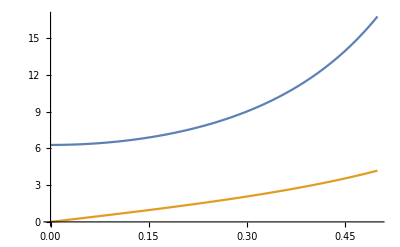

```mathematica
Plot[{NIntegrate[(1+Cos[2*ϕ])/(1-2*α*Cos[ϕ]+α^2)^(3/2), {ϕ, 0, 2*π}], NIntegrate[Cos[ϕ]/(1-2*α*Cos[ϕ]+α^2),{ϕ, 0, 2*π}]}, {α, 0, 0.5}]
```

```mathematica
NIntegrate[(1+Cos[2*ϕ])/(1-2*0.1*Cos[ϕ]+0.1^2)^(3/2), {ϕ, 0, 2*π}]/(2*π)
```

1.04194

```mathematica
FullSimplify[1 + Cos[2*ϕ]]
```

2 Cos[ϕ]^2

```mathematica
Integrate[1/(1-2*α*Cos[ϕ]+α^2)^(3/2), {ϕ, 0, 2*π}]
```

$Aborted

```mathematica
maxorder=4;
Terms={};
For[j5 = -maxorder, j5 ≤ maxorder, ++j5,
	j6range = (maxorder - Abs[j5]);
	For[j6 = -j6range, j6 ≤ j6range, ++j6,
		If[!EvenQ[j5 + j6], Continue[]];
		pmin = If[j5 + j6 < 0, IntegerPart[-(j5 + j6) / 2], 0];
		pprimemin = If[j5 + j6 < 0, 0, IntegerPart[(j5 + j6) / 2]];
		smin = Max[pmin, pprimemin, j6 + 2 * pmin, -j5 + 2 * pprimemin];
		j3range=j6range-Abs[j6];
		For[j3 = -j3range, j3 ≤ j3range, ++j3,
			j4range = j3range - Abs[j3];
			For[j4 = -j4range, j4 ≤ j4range, ++j4,
				imax = IntegerPart[(maxorder - Abs[j3] - Abs[j4]) / 2];
				For[i = 0, i ≤ imax, ++i,
					For[s = smin, s ≤ i, ++s,
						nmax = IntegerPart[(s - smin) / 2];
						For[n = 0, n ≤ nmax, ++n,
							For[m = 0, m ≤ (s - 2 * n), ++m,
								For[l = 0, l ≤ (i - s), ++l,
									twop = (-j6 - m + s - 2 * n);
									twopprime = (j5 - m + s - 2 * n);
									If[
										(
											!EvenQ[twop]
											||
											!EvenQ[twopprime]
											||
											twop > (2 * s - 4 * n)
											||
											twopprime > (2 * s - 4 * n)
											||
											twop < 2 * pmin
											||
											twopprime < 2 * pprimemin
										),
										Continue[]
									];
									p = IntegerPart[twop/2];
									pprime = IntegerPart[twopprime/2];
									j1 = (s - 2 * n - 2 * pprime - j3) + (i + j - 2 * l - s);
									j2 = -(s - 2 * n - 2 * p + j4) - (i + j - 2 * l - s);

									If[j1+j2+j3+j4+j5+j6==0,
										If[Abs[j1+j2]==0,
											If[j3==0 && j4==0 && j5==0 && j6==0, Print["Accepted i=", i, ", s=", s, ", n=", n, ", p=", p, ", p'=", pprime, ", m=", m]];
											If[j3>0,
												AppendTo[Terms, {j3,j4,j5,j6}],
												If[j3==0,
													If[j4>0,
														AppendTo[Terms, {j3,j4,j5,j6}],
														If[j4==0,
															If[j5≥0,
																AppendTo[Terms, {j3,j4,j5,j6}],
																AppendTo[Terms,{-j3,-j4,-j5,-j6}]
															],
															AppendTo[Terms,{-j3,-j4,-j5,-j6}]
														]
													],
													AppendTo[Terms,{-j3,-j4,-j5,-j6}]
												]	
											];
										]
									]
								]
							]
						]
					]
				]
			]
		]
	]
]
Sort[DeleteDuplicates[Terms]]
```

Accepted i=0, s=0, n=0, p=0, p'=0, m=0

Accepted i=1, s=0, n=0, p=0, p'=0, m=0

Accepted i=1, s=0, n=0, p=0, p'=0, m=0

Accepted i=1, s=1, n=0, p=0, p'=0, m=1

Accepted i=2, s=0, n=0, p=0, p'=0, m=0

Accepted i=2, s=0, n=0, p=0, p'=0, m=0

Accepted i=2, s=0, n=0, p=0, p'=0, m=0

Accepted i=2, s=1, n=0, p=0, p'=0, m=1

Accepted i=2, s=1, n=0, p=0, p'=0, m=1

Accepted i=2, s=2, n=0, p=1, p'=1, m=0

Accepted i=2, s=2, n=0, p=0, p'=0, m=2

Accepted i=2, s=2, n=1, p=0, p'=0, m=0

{{0,0,0,0},{0,0,1,-1},{0,0,2,-2},{0,2,-2,0},{0,2,-1,-1},{0,2,0,-2},{1,-1,-1,1},{1,-1,0,0},{1,-1,1,-1},{1,1,-2,0},{1,1,-1,-1},{1,1,0,-2},{2,-2,0,0},{2,0,-2,0},{2,0,-1,-1},{2,0,0,-2}}

```mathematica
f[x_]:=Module[{a}, a=x^2; result[y_]:=Print["a=", a,", x=", x, ", y=", y ]; Return[result]];
```

```mathematica
g=f[3]
```

result

```mathematica
g[5]
```

a=9, x=3, y=5